## Метод стационарной фазы Баталов С.А.

```mathematica
ClearAll["Global`*"]
```

### Условие задачи №7

,
сведем к комплексной экспоненте
,
теперь заметим, что  является стационарной точкой, поэтому использование формулы интегрирования по частям не даст истинного асимптотического разложения, однако ее можно будет задействовать, чтобы уточнить результат в первом приближении. Найдем пока нулевое приближение интеграла (его порядок будет меньше чем ), для этого перейдем к интегрированию по промежутку , используя свойство четности подынтегрального выражения и тот факт, что при  подынтегральная функция быстро периодически меняется, что гарантирует малость площади под ее графиком для больших 
,
однако теперь необходимо взять несобственный интеграл, для этого разложим в ряд по степеням  гиперболический синус и множитель  до первого члена в окрестности 0 (основной вклад подынтегральная функция вносит именно в окрестности 0), тогда получим

### Нулевое приближение

```mathematica
F0 = Simplify[Im[ComplexExpand[2 * Integrate[x * Exp[I * λ * x^3 / 6], {x, 0, Infinity}, Assumptions->{λ > 1}]]], Assumptions->{λ > 1}];
F0 // TraditionalForm
```

(2^(2/3) 3^(1/6) 2/3)/λ^(2/3)

### Первое приближение

Теперь уточним результат, используя формулу интегрирования по частям, применим ее к исходному выражению

```mathematica
ϕ = Sinh[x];
S = x - Sin[x];
ψ = Exp[I * λ * S];
f = ϕ * ψ;
```

```mathematica
DoubleSub := Simplify[(#1 /. {#2[[1]] -> #2[[3]]}) - (#1 /. {#2[[1]] -> #2[[2]]})] &;
PD := Simplify[(-1)^#2 * D[#1, {x, #2}] / (D[S, x] * λ * I)] &;
ImExpand := Simplify[Im[ComplexExpand[#]], Assumptions -> {λ > 1}] &;
```

```mathematica
F1 = ImExpand[DoubleSub[PD[ϕ, 0] * ψ, {x, -1, 1}]];
F1 // TraditionalForm
```

((ⅇ^2-1) cos(λ (sin(1)-1)))/(ⅇ λ (cos(1)-1))

### Ответ

```mathematica
F0 + F1 // TraditionalForm
```

(2^(2/3) 3^(1/6) 2/3)/λ^(2/3)+((ⅇ^2-1) cos(λ (sin(1)-1)))/(ⅇ λ (cos(1)-1))

### Сравнение с точным решением

Численно найдем значения интеграла для интересующих

```mathematica
NF := Im[NIntegrate[f /. {λ -> #}, {x, -1, 1}]] &;
```

Сравним приближенное решение с точным

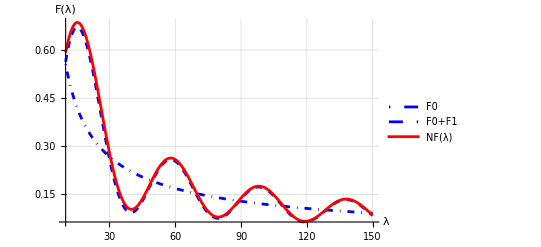

```mathematica
Plot[{F0, F0 + F1, NF[λ]}, {λ, 10, 150}, PlotLegends -> Placed["Expressions", Below], AxesLabel -> {λ, F[λ]}, 
	GridLines -> Automatic, PlotStyle -> {{Blue, DotDashed}, {Blue, Dashed}, Red}, PlotRange -> All]
```